#### Data

```mathematica
SeedRandom[1234];
SetDirectory[NotebookDirectory[]];
quoraquestions=SemanticImport["train.csv"];
quora=RandomSample[Join[quoraquestions[[All,5]],quoraquestions[[All,4]]],26654];
movie=StringSplit[Import["movie_lines.tsv","Text"],{"\t","\n"}];
lines=StringReplace[Partition[movie,5][[All,-1]],{"\""->""}];
linesJoined=StringJoin[Riffle[lines," "]];
sentences=TextCases[linesJoined,"Sentence"];
validChars = {"\t", "\n", " ", "!", "\"", "#", "$", "%", "&", "'", "(", ")", "*", "+", ",", "-", ".", "/", "0", "1", "2", "3", "4", "5", "6", 
    "7", "8", "9", ":", ";", "<", "=", ">", "?", "@", "A", "B", "C", "D", "E", "F", "G", "H", "I", "J", "K", "L", "M", "N", "O", "P", "Q", "R", 
    "S", "T", "U", "V", "W", "X", "Y", "Z", "[", "\\", "]", "^", "_", "`", "a", "b", "c", "d", "e", "f", "g", "h", "i", "j", "k", "l", "m", 
    "n", "o", "p", "q", "r", "s", "t", "u", "v", "w", "x", "y", "z", "{", "|", "}", "~"}; 
wikiSimport=Import["wikisentences1.mx"];
wikiS = StringDelete[wikiSimport, Except[validChars]];
questions=Join[Normal[quora],Select[sentences,StringContainsQ[#,"?"]&]];
questionsWithoutQuestions = StringReplace[questions,{"?"->"."}];
normalLines=Join[wikiS,RandomSample[Complement[sentences,questions][[80;;64213]],19653]];
```

```mathematica
classesqs=Thread[#->"Question"]&/@questionsWithoutQuestions;
classesnotqs=Thread[#->"Not a Question"]&/@normalLines;
(*classesJoined=Join[classesqs,classesnotqs];
training=RandomSample[classesJoined,20000];
validationset=RandomSample[Complement[classesJoined,training],2000];
testset=RandomSample[Complement[classesJoined,validationset,training],2000];*)
```

The data is loaded and divided into classes of questions and not questions!

```mathematica
classesnotqs//Length
```

46307

```mathematica
questions//Length
```

46307

```mathematica
normalLines//Length
```

46307

#### Changing parts of speech to numbers

```mathematica
rules = MapIndexed[#1 ->First[#2 ]&,{"Adjective","Adverb","Conjunction","Determiner","Interjection","Missing","Noun","Numeral","Particle","Preposition","Pronoun","ProperNoun","Punctuation","Symbol","Verb"}]
```

{Adjective→1,Adverb→2,Conjunction→3,Determiner→4,Interjection→5,Missing→6,Noun→7,Numeral→8,Particle→9,Preposition→10,Pronoun→11,ProperNoun→12,Punctuation→13,Symbol→14,Verb→15}

```mathematica
whQuestions = {"which"," what", "whose" , "who", "whom", "whose", "what", "which", "where","whither" ,"whence","when","how" ,"why" ,"whether","whatsoever"};
```

#### Changing parts of speech to numbers

```mathematica
vectorNumbers["How are you"]
```

{2,15,11}

```mathematica
numberPositionWh["What   are you where"]
```

1

```mathematica
(* creates a numerical sequence representing Parts Of Speech *)
vectorNumbers [ line_ ] := 
 (( TextStructure[line, "PartsOfSpeech"][[1,1,1,All,2,1]] ) 
     /. Missing[] -> {"","Missing"})[[All,2]] /. rules

(* gets position of WH Question *)
positionWh [line_ ] := StringContainsQ[ StringSplit[line] , whQuestions, IgnoreCase -> True]

(* gives the position of the first WH Question *)
numberPositionWh [ line_ ] := With[ {whPosition =Position[positionWh[ line ],True]} ,
                                    If[ Length[whPosition] >0 , whPosition[[1,1]],0]
                               ] 
(* Gives True if there is a WH Question as 1 or 0 *)
whQuestionsChecker [ line_ ] := StringContainsQ[ line , whQuestions, IgnoreCase -> True]
```

```mathematica
createClasses1D[ keyValuelines_List ] := Map[ { Keys[#],
                                                vectorNumbers[Keys[#]],
                                                numberPositionWh [ Keys[#] ]
                                               } 
                                                -> Values[#] 
                                             &,
                                             keyValuelines
                                            ]
                                            
                                            
createClasses3D[ keyValuelines_List ] := Map[ { Keys[#],
                                                vectorNumbers[Keys[#]],
                                                numberPositionWh [ Keys[#] ]
                                               } 
                                                -> Values[#] 
                                             &,
                                             keyValuelines
                                            ]
 
 (* 3D with Boolean field *)                                                                                      
createClasses3DBoolean[ keyValuelines_List ] := Map[ { Keys[#],
                                                vectorNumbers[Keys[#]],
                                                whQuestionsChecker [ Keys[#] ]
                                               } 
                                                -> Values[#] 
                                             &,
                                             keyValuelines
                                            ]
```

```mathematica
createClasses3DBoolean[ {"How are you"->"Question"," are you"->"Non Question" } ]
```

{{How are you,{2,15,11},True}→Question,{ are you,{15,11},False}→Non Question}

```mathematica
Classify[{{"How are you",{2,15,11},True}->"Question",{" are you",{15,11},False}->"Non Question"}]
```

ClassifierFunction[…]

```mathematica
SeedRandom[234];
classesqs2400=RandomSample[classesqs,2400]
classesnotqs2400=RandomSample[classesnotqs,2400]
```

```mathematica
classesq3D=createClasses3D [classesqs2400]
```

{{How come The Simpsons predicted things correctly (see the image).,{2,15,4,12,15,7,2,13,15,4,7,13,13},1}→Question,2398,{What was Ramanujan's IQ.,{11,15,12,12,13},1}→Question}
 |  |  |  |

```mathematica
createClasses3D[classesnotqs[[5;;7]]]
```

{{Artifice Books' first project, released in 2012, was "EXITS ARE," an e-book by Mike Meginnis (and many players), published in conjunction with Uncanny Valley.,{12,12,1,7,13,15,10,8,13,15,13,12,15,13,13,4,7,10,12,12,13,3,1,7,13,13,15,10,7,10,12,12,13},0}→Not a Question,{A toddler is a child 12 to 36 months old.,{4,7,15,4,7,8,10,8,7,1,13},0}→Not a Question,{The toddler years are a time of great cognitive, emotional and social development.,{4,7,7,15,4,7,10,1,1,13,1,3,1,7,13},0}→Not a Question}

```mathematica
classesnq3D=createClasses3D [classesnotqs2400]
```

$Aborted

```mathematica
train3DJoined=Join[classesq3D,classesnq3D]
train3D=RandomSample[train3DJoined,4000]
validationset=RandomSample[Complement[train3DJoined,train3D],300];
testset=RandomSample[Complement[train3DJoined,validationset,train3D],400];
```

{1}
 |  |  |  |

{1}
 |  |  |  |

#### Extracting all lines from scripts

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jofre/Documents/GitHub/Summer2018Zhamilya/Project 2018

```mathematica
data=StringSplit[Import["movie_lines.tsv","Text"],{"\t","\n"}];
```

```mathematica
lines=StringReplace[Partition[data,5][[All,-1]],{"\""->""}];
```

```mathematica
linesJoined=StringJoin[Riffle[lines," "]];
```

```mathematica
Riffle[lines," "]
```

```mathematica
lines//Length
```

304894

```mathematica
sentences=TextCases[linesJoined,"Sentence"];
```

#### Extracting and modifying questions from lines

Replacing “?” for “.” and making letters of lower case

```mathematica
questionsWithQuestionMark = Select[sentences,StringContainsQ[#,"?"]&]
```

{She okay?,You know how sometimes you just become this persona?,And you don't know how to quit?,Like my fear of wearing pastels?,What good stuff?,What crap?,19642,Well what's the point of waiting?,It's sixth century B.C.  Do you like the period?,Dance?,Okay?,What are you going to do?}
 |  |  |  |

```mathematica
questions=ToUpperCase[StringReplace[Select[sentences,StringContainsQ[#,"?"]&],{"?"->"."}]]
```

{SHE OKAY.,YOU KNOW HOW SOMETIMES YOU JUST BECOME THIS PERSONA.,AND YOU DON'T KNOW HOW TO QUIT.,LIKE MY FEAR OF WEARING PASTELS.,WHAT GOOD STUFF.,WHAT CRAP.,19642,WELL WHAT'S THE POINT OF WAITING.,IT'S SIXTH CENTURY B.C.  DO YOU LIKE THE PERIOD.,DANCE.,OKAY.,WHAT ARE YOU GOING TO DO.}
 |  |  |  |

#### Extracting and modifying normal sentences from lines

```mathematica
normalLines=ToUpperCase[Complement[sentences,questionsWithQuestionMark][[80;;64213]]]
```

{AAA!,AAAAAAAAAA!,AAAGH!,AAAHGHHH!,AAAWW SHIT!...,AAH!,A B...,A B-24 LIBERATOR.,64118,ZEKE.,ZERELDA DID.,ZERELDA IT'S NO COINCIDENCE.,ZERO...,ZERO DISTORTION SIR.,ZOD.,ZOE COME SAY HELLO TO YOUR FATHER..,ZOR-EL BUT WHAT CAN YOU A MERE GIRL- SUPERMAN WILL RETURN IT.}
 |  |  |  |

```mathematica
normalLines1=RandomSample[normalLines,19653]
```

{I DON'T THINK I'LL BE HAVING SEX EVER AGAIN.,BREE -- MY GOD I THOUGHT IT WAS OVER.,I GOTTA HAVE A JOB WHERE I COME TO WORK AT ELEVEN -- GO TO LUNCH AT TWELVE -- AND QUIT AT ONE.,19648,THE FIT ISN'T RIGHT.,THE BET'S OFF.}
 |  |  |  |

#### Random Sample

```mathematica
SeedRandom[1234];trainquestions1=RandomSample[questions,13757]
```

{DID YA GET THE LICENSE NUMBER.,YOU GONNA PULL.,WE'VE KNOWN DEBBIE WHAT SINCE THE EIGHTH GRADE.,JOYCE GIVE THE ASSISTANT CHIEF INSPECTOR A DRINK WOULD YOU.,13749,MISS WOLLSTEN SHARES THE ROOM WITH YOU.,WHAT DO YOU WANT TO KNOW EVAN.,WILL THESE BOARDS HOLD.,LIKE MY FEAR OF WEARING PASTELS.}
 |  |  |  |

```mathematica
SeedRandom[1234];trainnonquestions1=RandomSample[normalLines1,13757]
```

{JUST.,I HAVEN'T GOT NO CLASS.,AND I'LL BE OUTTA A JOB.,YOU'RE AN INSPIRATION LLOYD; YOU SHOULD GO ON THE SEVEN HUNDRED CLUB OR SOMETHING.,13749,I'M SORRY IF I SEEM OVER-ANXIOUS TO YOU.,YOU'RE UNDER AGE.,YOU NEWSHOUNDS'VE BEEN AFTER ME AND MY FOLKS EVER SINCE I WON THAT DUMB CONTEST.,THREE...}
 |  |  |  |

```mathematica
SeedRandom[1234];validationq1=RandomSample[Complement[questions,trainquestions1],2000];
```

```mathematica
SeedRandom[1234];validationnonq1=RandomSample[Complement[normalLines1,trainnonquestions1],2000];
```

```mathematica
SeedRandom[1234];testq1=RandomSample[Complement[questions,trainquestions1,validationq1],2600];
```

```mathematica
SeedRandom[1234];testnonq1=RandomSample[Complement[normalLines1,trainnonquestions1,validationnonq1],2600];
```

#### Classify

```mathematica
categories = Union[Flatten[Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,questions[[1;;1000]]]]]
```

```mathematica
partsOfSpeechNumbers [ x_] := Transpose[
{ x,
Map[
(
 (
  (
   (
     TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]]
    )/.Missing[]->{"","Missing"}
   )
  )
  [[All,2]]
) 
& , x ]
/. rules}] ;

createClasses [ x_] := Transpose[
{ x,
Map[
(
 (
  (
   (
     TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]]
    )/.Missing[]->{"","Missing"}
   )
  )
  [[All,2]]
) 
& , x ]
/. rules,

whQuestionsChecker [ x ]/.{True->1,False ->0}}] ;
```

```mathematica
Transpose[{questions[[1;;10]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,questions[[1;;10]]]/.rules}]
```

{{SHE OKAY.,{12,12,13}},{YOU KNOW HOW SOMETIMES YOU JUST BECOME THIS PERSONA.,{11,15,7,2,11,2,15,7,7,13}},{AND YOU DON'T KNOW HOW TO QUIT.,{3,11,15,2,12,12,10,12,13}},{LIKE MY FEAR OF WEARING PASTELS.,{10,12,7,10,15,7,13}},{WHAT GOOD STUFF.,{4,1,7,13}},{WHAT CRAP.,{4,7,13}},{DO YOU LISTEN TO THIS CRAP.,{12,11,15,10,12,12,13}},{YOU ALWAYS BEEN THIS SELFISH.,{11,2,15,7,1,13}},{YOU NEVER WANTED TO GO OUT WITH 'ME DID YOU.,{11,2,15,10,12,12,10,13,12,12,11,13}},{I WAS.,{11,15,13}}}

```mathematica
cl=Classify[<|"Question"-> Transpose[{questions[[1;;1000]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,questions[[1;;1000]]]}], "Not Question"->Transpose[{normalLines1[[1;;1000]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,normalLines1[[1;;1000]]]}]|> ,ValidationSet-><|"Question"-> Transpose[{validationq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationq1[[1;;100]]]}], "Not Question"->Transpose[{validationnonq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationnonq1[[1;;100]]]}] |>]
```

```mathematica
cl=Classify[<|"Question"-> Transpose[{questions[[1;;500]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,questions[[1;;500]]]}], "Not Question"->Transpose[{normalLines1[[1;;500]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,normalLines1[[1;;500]]]}]|> ,ValidationSet-><|"Question"-> Transpose[{validationq1[[1;;50]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationq1[[1;;50]]]}], "Not Question"->Transpose[{validationnonq1[[1;;50]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationnonq1[[1;;50]]]}] |>,PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

```mathematica
cm =ClassifierMeasurements[cl,<|"Question"-> Transpose[{testq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,testq1[[1;;100]]]}], "Not Question"->Transpose[{testnonq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,testnonq1[[1;;100]]]}] |>]
```

ClassifierMeasurementsObject[…]

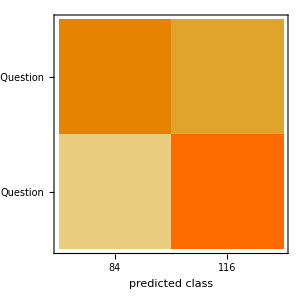

```mathematica
cm["ConfusionMatrixPlot"]
```

### With Vector Numbers

```mathematica
rules = MapIndexed[#1 ->First[#2 ]&,{"Adjective","Adverb","Conjunction","Determiner","Interjection","Missing","Noun","Numeral","Particle","Preposition","Pronoun","ProperNoun","Punctuation","Symbol","Verb"}]
```

{Adjective→1,Adverb→2,Conjunction→3,Determiner→4,Interjection→5,Missing→6,Noun→7,Numeral→8,Particle→9,Preposition→10,Pronoun→11,ProperNoun→12,Punctuation→13,Symbol→14,Verb→15}

```mathematica
cl=Classify[<|"Question"-> Transpose[{questions[[1;;500]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,questions[[1;;500]]]/.rules}], "Not Question"->Transpose[{normalLines1[[1;;500]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,normalLines1[[1;;500]]]/.rules}]|> ,ValidationSet-><|"Question"-> Transpose[{validationq1[[1;;50]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationq1[[1;;50]]]/.rules}], "Not Question"->Transpose[{validationnonq1[[1;;50]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,validationnonq1[[1;;50]]]/.rules}] |>,PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

```mathematica
cm =ClassifierMeasurements[cl,<|"Question"-> Transpose[{testq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,testq1[[1;;100]]]/.rules}], "Not Question"->Transpose[{testnonq1[[1;;100]],Map[((((TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]])/.Missing[]->{"","Missing"}))[[All,2]])& ,testnonq1[[1;;100]]]/.rules}] |>]
```

ClassifierMeasurementsObject[…]

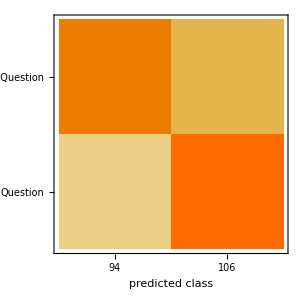

```mathematica
cm["ConfusionMatrixPlot"]
```

### Classify with 1000 sentences per class

```mathematica
partsOfSpeechNumbers [ questions[[1;;100]] ]
```

```mathematica
cl1000=Classify[

<|
"Question"-> 
partsOfSpeechNumbers[ questions[[1;;2000]]],

"Not Question"-> partsOfSpeechNumbers[ normalLines1[[1;;2000]]] |> ,

ValidationSet-><|"Question"-> partsOfSpeechNumbers[ validationq1[[1;;200]]],

 "Not Question"->partsOfSpeechNumbers[ validationnonq1[[1;;200]]] |>,

PerformanceGoal->"Speed"]
```

ClassifierFunction[…]

```mathematica
cl1000
```

```mathematica
cm =ClassifierMeasurements[cl1000,<|"Question"-> partsOfSpeechNumbers [ testq1[[1;;500]]], "Not Question"->  partsOfSpeechNumbers[testnonq1[[1;;500]]]|>]
```

ClassifierMeasurementsObject[…]

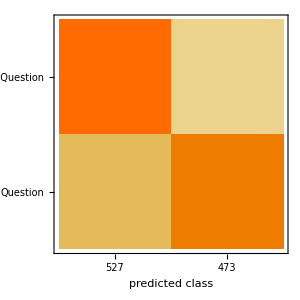

```mathematica
cm["ConfusionMatrixPlot"]
```

### 5000

```mathematica
cl5000=Classify[

<|
"Question"-> 
partsOfSpeechNumbers[ questions[[1;;5000]]], 
"Not Question"-> partsOfSpeechNumbers[ normalLines1[[1;;5000]]] |> ,

ValidationSet-><|"Question"-> partsOfSpeechNumbers[ validationq1[[1;;500]]],

 "Not Question"->partsOfSpeechNumbers[ validationnonq1[[1;;500]]] |>,

PerformanceGoal->"Speed"]
```

### 200

```mathematica
cl200=Classify[

<|
"Question"-> 
partsOfSpeechNumbers[ questions[[1;;1000]]], 
"Not Question"-> partsOfSpeechNumbers[ normalLines1[[1;;1000]]] |> ,

ValidationSet-><|"Question"-> partsOfSpeechNumbers[ validationq1[[1;;100]]],

 "Not Question"->partsOfSpeechNumbers[ validationnonq1[[1;;100]]] |>]
```

ClassifierFunction[…]

```mathematica
cm =ClassifierMeasurements[cl200,<|"Question"-> partsOfSpeechNumbers [ testq1[[1;;50]]], "Not Question"->  partsOfSpeechNumbers[testnonq1[[1;;50]]]|>]
```

ClassifierMeasurementsObject[…]

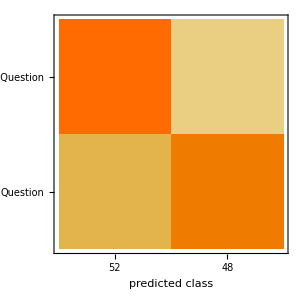

```mathematica
cm["ConfusionMatrixPlot"]
```

### 1000

```mathematica
cl1000=Classify[

<|
"Question"-> 
partsOfSpeechNumbers[ questions[[1;;1000]]], 
"Not Question"-> partsOfSpeechNumbers[ normalLines1[[1;;1000]]] |> ,

ValidationSet-><|"Question"-> partsOfSpeechNumbers[ validationq1[[1;;100]]],

 "Not Question"->partsOfSpeechNumbers[ validationnonq1[[1;;100]]] |>]
```

ClassifierFunction[…]

```mathematica
cm =ClassifierMeasurements[cl1000,<|"Question"-> partsOfSpeechNumbers [ testq1[[1;;500]]], "Not Question"->  partsOfSpeechNumbers[testnonq1[[1;;500]]]|>]
```

ClassifierMeasurementsObject[…]

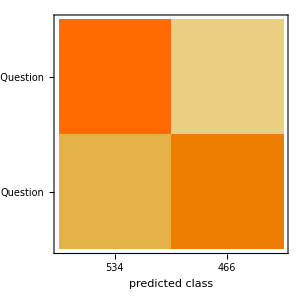

```mathematica
cm["ConfusionMatrixPlot"]
```

### Wh - question s

```mathematica
whQuestions = {"which"," what", "whose" , "who", "whom", "whose", "what", "which", "where","whither" ,"whence","when","how" ,"why" ,"whether","whatsoever"};
```

```mathematica
StringContainsQ["which", whQuestions]
```

True

```mathematica
vectorNumbers [ lines_ ] := Map[
 (((( TextStructure[#,"PartsOfSpeech"][[1,1,1,All,2,1]] ) 
     /. Missing[] -> {"","Missing"}))[[All,2]]) & ,
 lines
 ]
 
whQuestionsChecker [ lines_ ] := StringContainsQ[lines, whQuestions, IgnoreCase->True]
```

```mathematica
whQuestionsChecker [ testq1[[1;;100]] ]/.{True->1,False ->0}
```

{0,0,0,1,0,1,1,1,0,1,0,0,0,0,0,0,1,1,1,1,0,0,1,1,1,0,0,0,0,0,1,1,0,0,1,0,1,0,0,1,0,0,0,1,1,1,1,1,1,0,1,0,1,0,0,0,1,1,1,0,0,0,0,1,1,1,1,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,0,1,0,0,1,0,1,0,1,0,0,0,0,1,0,0,0}

### 1000

```mathematica
cl1000=Classify[

<|
"Question"-> 
createClasses[ questions[[1;;5000]]], 

"Not Question"-> createClasses[ normalLines1[[1;;5000]]] |> ,

ValidationSet-><|"Question"-> createClasses[ validationq1[[1;;300]]],

 "Not Question"->createClasses[ validationnonq1[[1;;300]]] |>]
```

ClassifierFunction[…]

```mathematica
cm =ClassifierMeasurements[cl200,<|"Question"-> createClasses [ testq1[[1;;200]]], "Not Question"->  createClasses[testnonq1[[1;;200]]]|>]
```

ClassifierMeasurementsObject[…]

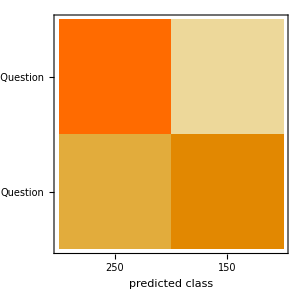

```mathematica
cm["ConfusionMatrixPlot"]
```

### 5000

```mathematica
cl1000=Classify[

<|
"Question"-> 
createClasses[ questions[[1;;5000]]], 

"Not Question"-> createClasses[ normalLines1[[1;;5000]]] |> ,

ValidationSet-><|"Question"-> createClasses[ validationq1[[1;;300]]],

 "Not Question"->createClasses[ validationnonq1[[1;;300]]] |>]
```

Java::excptn: A Java exception occurred: java.lang.OutOfMemoryError: Java heap space
	at edu.stanford.nlp.trees.LabeledScoredTreeFactory.newTreeNode(LabeledScoredTreeFactory.java:56)
	at edu.stanford.nlp.parser.common.ParserUtils.xTree(ParserUtils.java:41)
	at edu.stanford.nlp.parser.lexparser.LexicalizedParser.parse(LexicalizedParser.java:313)
	at edu.stanford.nlp.parser.common.ParserGrammar.parse(ParserGrammar.java:84)
	at sun.reflect.GeneratedMethodAccessor8.invoke(Unknown Source).

Table::iterb: Iterator {MachineLearning`Models`GrammaticalParser`Private`i,$Failed[MachineLearning`Models`GrammaticalParser`Private`numChildren[]]} does not have appropriate bounds.

ClassifierFunction[…]

```mathematica
cm =ClassifierMeasurements[cl200,<|"Question"-> createClasses [ testq1[[1;;500]]], "Not Question"->  createClasses[testnonq1[[1;;500]]]|>]
```

ClassifierMeasurementsObject[…]

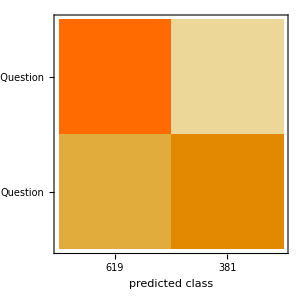

```mathematica
cm["ConfusionMatrixPlot"]
```

### 4000 + 5W1H parameter

```mathematica
cl40003D=Classify[train3D,ValidationSet->validationset]
```

ClassifierFunction[…]

```mathematica
cm40003D =ClassifierMeasurements[cl40003D,testset]
```

ClassifierMeasurementsObject[…]